```mathematica
PartitionGraph[s_]:=Block[{result={},todo={},i,j, bucket,pos},
If[Length[s]==1,
Return[{}]
,
For[i=1,i≤Length[s],i++,
For[j=i+1,j≤Length[s],j++,
bucket=ReverseSort[Append[Delete[Delete[s,j],i],s[[i]]+s[[j]]]];
If[!MemberQ[todo,bucket],
AppendTo[result,s->bucket];
AppendTo[todo,bucket]
]
];
];
For[pos=1,pos≤Length[todo],pos++,
result=DeleteDuplicates[Join[result,PartitionGraph[todo[[pos]]]]]
];
result
]
];
```

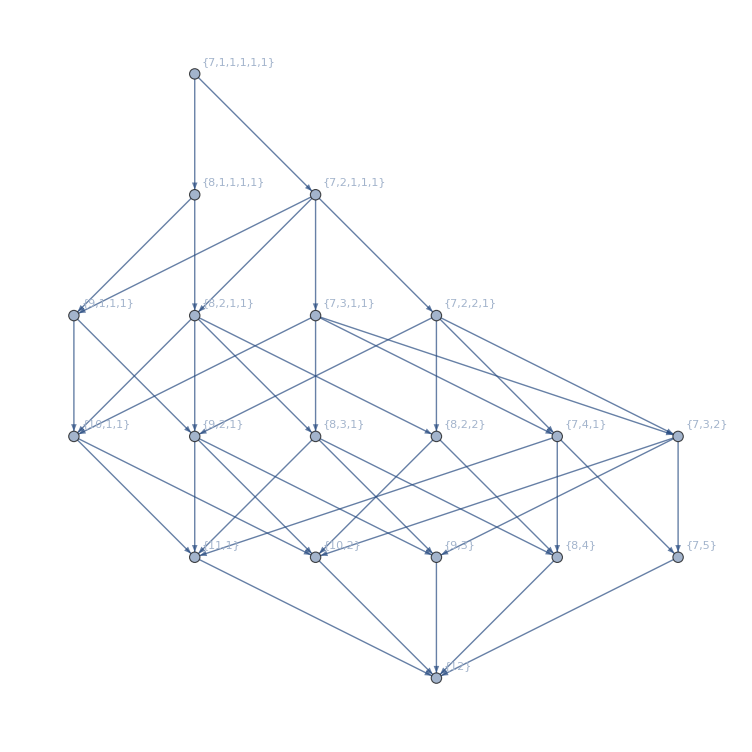

```mathematica
Graph[PartitionGraph[{7,1,1,1,1,1}],VertexLabels->"Name"]
```

```mathematica
Union
```

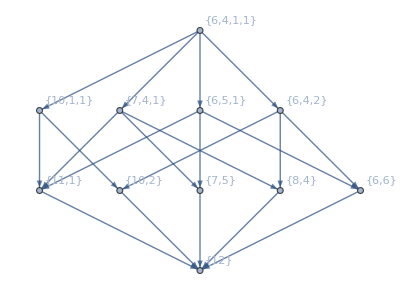

```mathematica
Graph[PartitionGraph[{6,4,1,1}],VertexLabels->"Name"]
```

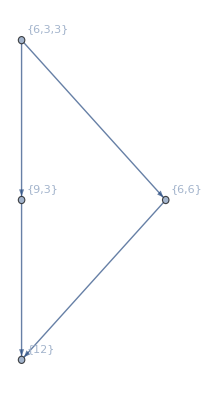

```mathematica
Graph[PartitionGraph[{6,3,3}],VertexLabels->"Name"]
```

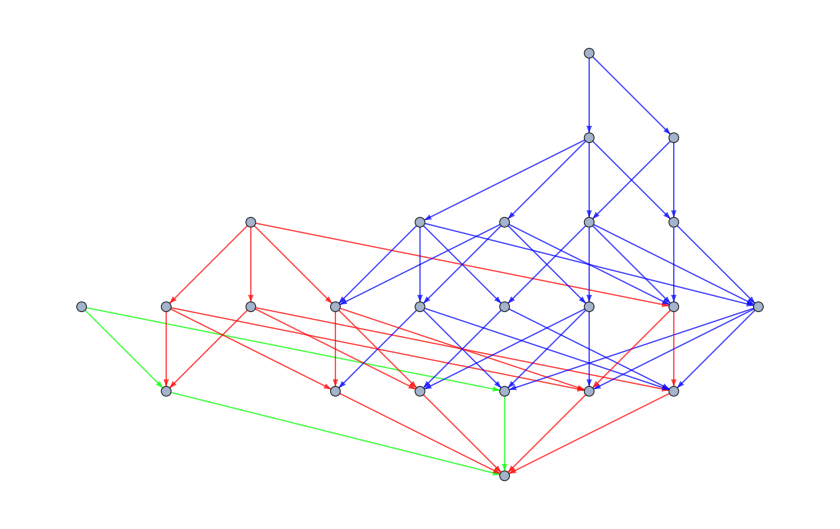

```mathematica
With[{g=Graph[PartitionGraph[{7,1,1,1,1,1}],VertexLabels->"Name"],
h=Graph[PartitionGraph[{6,4,1,1}],VertexLabels->"Name"],
i=Graph[PartitionGraph[{6,3,3}],VertexLabels->"Name"]},
GraphUnion[g,h,i,
EdgeStyle->Join[
Map[#->Blue&,EdgeList[g]],
Map[#->Red&,EdgeList[h]],
Map[#->Green&,EdgeList[i]]
]
]
]
```

```mathematica
GraphLaplacian[ReadGrof[9]]//Tr
```

30

```mathematica
ListofVars[allGraphs5[lambdaKey,"colofour"]]
```

{v13x24x5,v13x25x4,v13x2x4x5,v14x25x3,v14x2x35,v14x2x3x5,v1x24x35,v1x24x3x5,v1x25x3x4,v1x2x35x4,v1x2x3x4x5}

```mathematica
SetsToSymbol[Map[{#}&,PartitionType[SymbolToSets[v14x2x35]]]]
```

v2x2x1

```mathematica
Map[SetsToSymbol[Map[{#}&,PartitionType[SymbolToSets[#]]]]&,ListofVars[allGraphs5[lambdaKey,"colofour"]]]//Total
```

v1x1x1x1x1+5 v2x1x1x1+5 v2x2x1

```mathematica
Table[
Total[Map[SetsToSymbol[Map[{#}&,PartitionType[SymbolToSets[#]]]]&,ListofVars[allGraphs5[k,"colofour"]]]],
{k,allGraphs5NullAtomKeys}
]//Tally//Sort//TableForm
```

v5 | 1
v3x2+v5 | 10
v4x1+v5 | 5
v2x2x1+2 v3x2+v4x1+v5 | 15
v3x1x1+v3x2+2 v4x1+v5 | 10
v2x1x1x1+3 v2x2x1+3 v3x1x1+4 v3x2+3 v4x1+v5 | 10
v1x1x1x1x1+10 v2x1x1x1+15 v2x2x1+10 v3x1x1+10 v3x2+5 v4x1+v5 | 1

```mathematica
allGraphs6=Get["d:\\saved\\allGraphs6-fullfullgen.m"];
```

```mathematica
Table[
Total[Map[SetsToSymbol[Map[{#}&,PartitionType[SymbolToSets[#]]]]&,ListofVars[allGraphs6[k,"colofour"]]]],
{k,allGraphs6GeneratorAtomKeys}
]//Tally//Sort//TableForm
```

v1x1x1x1x1x1 | 1
v1x1x1x1x1x1+v2x1x1x1x1 | 15
v1x1x1x1x1x1+2 v2x1x1x1x1+v2x2x1x1 | 45
v1x1x1x1x1x1+3 v2x1x1x1x1+3 v2x2x1x1+v2x2x2 | 15
v1x1x1x1x1x1+3 v2x1x1x1x1+v3x1x1x1 | 20
v1x1x1x1x1x1+4 v2x1x1x1x1+3 v2x2x1x1+v3x1x1x1+v3x2x1 | 60
v1x1x1x1x1x1+6 v2x1x1x1x1+9 v2x2x1x1+2 v3x1x1x1+6 v3x2x1+v3x3 | 10
v1x1x1x1x1x1+6 v2x1x1x1x1+3 v2x2x1x1+4 v3x1x1x1+v4x1x1 | 15
v1x1x1x1x1x1+7 v2x1x1x1x1+9 v2x2x1x1+3 v2x2x2+4 v3x1x1x1+4 v3x2x1+v4x1x1+v4x2 | 15
v1x1x1x1x1x1+10 v2x1x1x1x1+15 v2x2x1x1+10 v3x1x1x1+10 v3x2x1+5 v4x1x1+v5x1 | 6
v1x1x1x1x1x1+15 v2x1x1x1x1+45 v2x2x1x1+15 v2x2x2+20 v3x1x1x1+60 v3x2x1+10 v3x3+15 v4x1x1+15 v4x2+6 v5x1+v6 | 1

```mathematica
Table[
Total[Map[SetsToSymbol[Map[{#}&,PartitionType[SymbolToSets[#]]]]&,ListofVars[allGraphs6[k,"colofour"]]]],
{k,allGraphs6FakeAtomKeys}
]//Tally//Sort//TableForm
```

v1x1x1x1x1x1 | 1
v1x1x1x1x1x1+5 v2x1x1x1x1 | 6
v1x1x1x1x1x1+8 v2x1x1x1x1+12 v2x2x1x1 | 15
v1x1x1x1x1x1+9 v2x1x1x1x1+18 v2x2x1x1+6 v2x2x2 | 10
v1x1x1x1x1x1+9 v2x1x1x1x1+12 v2x2x1x1+4 v3x1x1x1 | 15
v1x1x1x1x1x1+11 v2x1x1x1x1+24 v2x2x1x1+6 v2x2x2+6 v3x1x1x1+12 v3x2x1 | 60
v1x1x1x1x1x1+12 v2x1x1x1x1+30 v2x2x1x1+8 v2x2x2+8 v3x1x1x1+24 v3x2x1+4 v3x3 | 15
v1x1x1x1x1x1+12 v2x1x1x1x1+27 v2x2x1x1+6 v2x2x2+10 v3x1x1x1+18 v3x2x1+3 v4x1x1 | 20
v1x1x1x1x1x1+13 v2x1x1x1x1+34 v2x2x1x1+10 v2x2x2+12 v3x1x1x1+32 v3x2x1+4 v3x3+4 v4x1x1+4 v4x2 | 45
v1x1x1x1x1x1+14 v2x1x1x1x1+39 v2x2x1x1+12 v2x2x2+16 v3x1x1x1+44 v3x2x1+6 v3x3+9 v4x1x1+8 v4x2+2 v5x1 | 15
v1x1x1x1x1x1+15 v2x1x1x1x1+45 v2x2x1x1+15 v2x2x2+20 v3x1x1x1+60 v3x2x1+10 v3x3+15 v4x1x1+15 v4x2+6 v5x1+v6 | 1

```mathematica
Table[
Total[Map[SetsToSymbol[Map[{#}&,PartitionType[SymbolToSets[#]]]]&,ListofVars[allGraphs6[k,"colofour"]]]],
{k,allGraphs6NullAtomKeys}
]//Tally//Sort//TableForm
```

v6 | 1
v3x3+v6 | 10
v4x2+v6 | 15
v2x2x2+3 v4x2+v6 | 15
v5x1+v6 | 6
v3x2x1+v3x3+v4x2+v5x1+v6 | 60
v4x1x1+v4x2+2 v5x1+v6 | 15
v2x2x1x1+v2x2x2+4 v3x2x1+2 v3x3+v4x1x1+3 v4x2+2 v5x1+v6 | 45
v3x1x1x1+3 v3x2x1+v3x3+3 v4x1x1+3 v4x2+3 v5x1+v6 | 20
v2x1x1x1x1+6 v2x2x1x1+3 v2x2x2+4 v3x1x1x1+16 v3x2x1+4 v3x3+6 v4x1x1+7 v4x2+4 v5x1+v6 | 15
v1x1x1x1x1x1+15 v2x1x1x1x1+45 v2x2x1x1+15 v2x2x2+20 v3x1x1x1+60 v3x2x1+10 v3x3+15 v4x1x1+15 v4x2+6 v5x1+v6 | 1

```mathematica
Table[
Total[Map[SetsToSymbol[Map[{#}&,PartitionType[SymbolToSets[#]]]]&,ListofVars[allGraphs6[k,"colofour"]]]],
{k,allGraphs6AtomKeys}
]//Tally//Sort//TableForm
```

v1x1x1x1x1x1 | 1
v2x1x1x1x1 | 15
v2x2x1x1 | 45
v2x2x2 | 15
v3x1x1x1 | 20
v3x2x1 | 60
v3x3 | 10
v4x1x1 | 15
v4x2 | 15
v5x1 | 6
v6 | 1